## De Bruijn

```mathematica
$HistoryLength=0;
```

```mathematica
{DeBruijnGraph[2,2],DeBruijnGraph[2,3],DeBruijnGraph[2,4]}
```

{-Graphics-,-Graphics-,-Graphics-}

On peut construire nous - meme ... un noeud i est relie a i + -1 %2^d

```mathematica
bru[d_]:=Graph[
Flatten[Table[{i->Mod[2i,2^d],i->Mod[2i+1,2^d]},{i,0,2^d-1}]],
VertexLabels->Table[i->StringJoin @@ ToString /@ PadLeft[IntegerDigits[i,2],d],{i,0,2^d-1}]
]
```

```mathematica
bru[4]
```

-Graphics-

#### Generer le pattern

```mathematica
permuteGraph[g_]:=Module[{nodes,edges},(
nodes=VertexList[g];
edges=RandomSample[EdgeList[g]];
Graph[nodes,edges]
)];
```

```mathematica
seq[p_,d_,base_]:=Join[
PadLeft[IntegerDigits[p[[1,1]]-1,base],d],
IntegerDigits[#,base][[-1]]& /@ (p[[All,2]]-1)
];
seq[p_,d_]:=seq[p,d,2];
```

Elimine les codes qui contiennent des doublons

```mathematica
p={0,1}
```

{0,1}

```mathematica
Delete[Abs[p-RotateLeft[p]],-1]
```

{1}

Dit si les elements de p sont sequentiellement au moins different de dist ou plus.

```mathematica
proche[p_,dist_]:=Length[Select[Delete[Abs[p-RotateLeft[p]],-1],(#< dist)&]]≥1
```

```mathematica
proche[{0,1,4},2]
```

True

Mettre dist = 0 pour garder tout, dist = 1 pour eliminer les bandes larges, dist = 2 + pour augmenter le contraste

```mathematica
singleBand[g_,base_,d_,dist_]:=VertexDelete[g,Select[Table[i,{i,0,base^d-1}],(proche[IntegerDigits[#,base,d],dist])& ]+1];
```

Genere nb sequences de longueur d

```mathematica
sequence[d_,nb_]:=seq[#,d]& /@ FindEulerianCycle[DeBruijnGraph[2,d],nb];
```

```mathematica
sequence[d_,nb_,base_]:=seq[#,d,base]& /@ FindEulerianCycle[DeBruijnGraph[base,d],nb];
```

```mathematica
sequenceSingleBand[d_,nb_,base_,dist_]:=seq[#,d,base]& /@ FindEulerianCycle[permuteGraph[singleBand[DeBruijnGraph[base,d],base,d,dist]],nb];
```

```mathematica
g=DeBruijnGraph[8,2]
```

-Graphics-

```mathematica
permuteGraph[g]
```

-Graphics-

```mathematica
gg=singleBand[g,8,2,2]
```

-Graphics-

#### Verification

Chaque nombre devrait apparaitre une fois.

```mathematica
positions[s_,d_,base_]:=FromDigits[#,base]& /@ Partition[s,d+1,1];
positions[s_,d_]:=positions[s,d,2];

check[s_,d_]:=Sort[positions[s,d]];
check[s_,d_,base_]:=Sort[positions[s,d,base]];
```

On veux 4 sequences de longueur d

```mathematica
s=sequence[3,100]
```

{{0,0,0,0,1,0,0,1,1,0,1,0,1,1,1,1,0,0,0},{0,0,1,0,0,0,0,1,1,0,1,0,1,1,1,1,0,0,1},{0,1,0,0,0,0,1,0,1,1,0,0,1,1,1,1,0,1,0},{0,1,1,0,0,0,0,1,0,0,1,1,1,1,0,1,0,1,1},{1,0,0,0,0,1,0,0,1,1,0,1,0,1,1,1,1,0,0},{1,0,1,0,0,0,0,1,0,1,1,0,0,1,1,1,1,0,1},{1,1,0,0,0,0,1,0,0,1,1,0,1,0,1,1,1,1,0},{1,1,1,0,0,0,0,1,0,0,1,1,0,1,0,1,1,1,1}}

Les sequences en string

```mathematica
(StringJoin @@ ToString /@ #)& /@ s // MatrixForm
```

(0000100110101111000
0010000110101111001
0100001011001111010
0110000100111101011
1000010011010111100
1010000101100111101
1100001001101011110
1110000100110101111)

```mathematica
check[#,3]& /@ s
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}}

#### Un test en couleur ...

```mathematica
s=sequence[2,1,8];
```

```mathematica
s=sequenceSingleBand[2,1000,8,1];
Dimensions[s]
is=ImageAdjust[Image[s],0,{0,7},{0,0.8}]
```

{56,394}

-Graphics-

```mathematica
s[[1]]
```

{0,1,2,6,4,3,7,1,2,4,3,5,3,7,0,1,5,1,3,2,0,3,2,7,4,3,0,6,2,5,3,6,7,6,2,6,3,0,7,6,5,7,1,0,7,4,2,6,0,1,0,3,1,5,0,3,7,5,0,4,1,3,1,7,1,5,6,4,6,1,4,5,7,5,7,0,7,5,4,5,0,6,3,1,2,5,7,3,1,6,1,5,2,0,2,6,2,0,1,6,0,5,7,4,6,5,4,3,6,4,5,4,2,7,3,2,4,7,1,6,4,7,2,7,0,6,5,6,1,3,0,2,4,6,4,1,2,7,1,3,6,5,3,1,4,3,4,7,3,6,1,2,0,7,1,4,2,1,7,3,7,6,3,4,3,1,3,5,2,4,2,0,6,4,2,4,5,6,2,1,2,1,0,1,4,6,0,7,0,2,3,2,5,1,7,0,3,6,3,5,0,5,0,2,7,5,1,6,7,3,4,1,7,2,1,5,4,0,3,0,1,7,4,5,2,3,7,4,1,0,6,0,4,2,3,5,1,2,3,0,5,6,0,2,1,3,7,3,0,4,0,4,6,7,5,2,7,2,3,1,0,2,5,2,1,4,1,4,0,7,3,5,4,6,3,2,6,1,0,4,5,1,5,3,0,3,4,0,2,0,4,3,2,3,4,6,2,7,6,0,3,5,7,6,1,7,5,6,7,1,7,6,7,0,4,7,5,3,4,2,5,0,1,3,4,5,3,2,1,6,5,1,0,5,4,7,0,5,2,6,7,4,7,4,0,6,7,2,0,5,3,5,6,3,7,2,6,5,0,7,2,5,6,5,2,5,4,1,5,7,2,4,1,6,2,3,6,0,6,1,6,3,6,2,4,0,5,1,4,7,6,4,0,1}

```mathematica
ss=s;
```

```mathematica
colors=Table[{i,i,i},{i,0,7}]/7.;
colors=Table[ColorConvert[{i/7*0.8,1,1},"RGB",ColorSpace->"HSB"],{i,0,7}];
colors=Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2];
```

```mathematica
ssc=Map[(colors[[#+1]])&, ss,{2}];
izd=ssc[[1;;8,1;;100]];
```

```mathematica
allonge[ligne_,mult_,shift_]:=RotateLeft[Flatten[Table[#,{i,mult}]& /@ ligne,1],shift];
```

```mathematica
izdgros=Table[allonge[izd[[i]],8,i-1],{i,1,Length[izd]}];
```

```mathematica
Dimensions[izdgros]
```

{8,800,3}

```mathematica
Image[izdgros[[1;;1]]]
```

-Graphics-

```mathematica
iz=ImageResize[Image[{#}],{800,600},Resampling->"Nearest"]& /@ izdgros;
Show[#,ImageSize->{800,600}]& /@ iz
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Un plus gros exemple ...

```mathematica
s=sequence[8,30];
```

```mathematica
(StringJoin @@ ToString /@ #)& /@ s // MatrixForm
```

(0000000001000000011000000101000000111000001001000001011000001101000001111000010001000010011000010101000010111000011001000011011000011101000011111000100011000100101000100111000101001000101011000101101000101111000110011000110101000110111000111001000111011000111101000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100000000
0000000100000000011000000101000000111000001001000001011000001101000001111000010001000010011000010101000010111000011001000011011000011101000011111000100011000100101000100111000101001000101011000101101000101111000110011000110101000110111000111001000111011000111101000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100000001
0000001000000000101000000110000000111000001001000001011000001101000001111000010001000010011000010101000010111000011001000011011000011101000011111000100011000100101000100111000101001000101011000101101000101111000110011000110101000110111000111001000111011000111101000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100000010
0000001100000000010000000111000000101000001001000001101000010001000010101000011001000011101000100101000101001000101100000101101000110001000110101000111001000111100000111101001001001100001001101001010101001011001001011100001011101001100101001101100001101101001110001001110101001111001001111100001111101010101100010101101010111001010111100010111101011001100011001101011011001011011100011011101011101100011101101011111001011111100011111101100111001100111101101101111001101111101110011101110111101111111001111111110100000011
0000010000000001001000001010000001011000000011000001101000001110000001111000010001000010011000010101000010111000011001000011011000011101000011111000100011000100101000100111000101001000101011000101101000101111000110011000110101000110111000111001000111011000111101000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100000100
0000010100000000010000001011000000011000001001000001101000010001000010101000011001000011100000011101000100101000101001000101101000110001000110101000111001000111100000111101001001001100001001101001010101001011001001011100001011101001100101001101100001101101001110001001110101001111001001111100001111101010101100010101101010111001010111100010111101011001100011001101011011001011011100011011101011101100011101101011111001011111100011111101100111001100111101101101111001101111101110011101110111101111111001111111110100000101
0000011000000000100000001101000000101000001001000001110000001111000001011000010001000010011000011001000011011000100011000101001000101010000101011000110011000111001000111010000111011001001001010001001011001010011001011010001011011001101001001101010001101011001110001001110011001111001001111010001111011010011011010101001010101011010111000010111001010111010010111011011011100011011101010011101011011110001011110011011111000011111001011111010011111011100111011101111010101111011111100011111101011111110011111111101100000110
0000011100000000010000000110000001010000001111000001001000001011000001101000010001000010101000011001000011101000100101000101001000101101000110001000110101000111001000111101001001001100001001101001010101001011001001011100001011101001100101001101100001101101001110001001110101001111001001111100001111101010101100010101101010111001010111100010111101011001100011001101011011001011011100011011101011101100011101101011111001011111100011111101100111001100111101101101111001101111101110011101110111101111111001111111110100000111
0000100000000010001000010010000010011000000011000010100000010101000010110000010111000000111000011001000011010000011011000011101000011110000011111000100011000100101000100111000101001000101011000101101000101111000110011000110101000110111000111001000111011000111101000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100001000
0000100100000000010000010011000000011000010001000010100000010101000011001000011100000011101000001101000100101000101001000101100000101101001001001101001100101001101100001101101010001100010001101010100101010101100010101101011001001011001100011001101011100001011100100011100101011101001011101100011101101100101101101110001001110001101110101001110101101111000001111000101111001001111001100111001101111100001111100101111101000111101001111101100111101110011101110111101010111111000111111011111110011111111101011110110100001001
0000101000000000100000010101000010001000010110000000110000010010000010111000000111000010011000011001000011010000011011000100011000101001000101011000110011000111001000111010000111011001001001010001001011001010011001011010001011011001101001001101010001101011001110001001110011001111000001111001001111010001111011010011011010101001010101011010111001010111010010111011011011100011011101010011101011011110001011110011011111000011111001011111010011111011100111011101111010101111011111100011111101011111110011111111101100001010
0000101100000000010000000110000010010000010100000010111000000111000010001000010011000010101000011001000011101000001101000100101000101001000101101001001001101001100101001101100001101101010001100010001101010100101010101100010101101011001001011001100011001101011100100011100101011101001011101100011101101100101101101110001001110001101110101001110101101111000001111000101111001001111001100111001101111100001111100101111101000111101001111101100111101110011101110111101010111111000111111011111110011111111101011110110100001011
0000110000000001000000011001000001001000010001000011010000001010000011011000001011000010011000011100000011101000010101000011110000011111000010111000100011000100101000100111000110011000110101000110111001000101001000111001010011001010101001010110001010111001100111001110101001110110001110111010010010011010010110010010111010110011010110100010110101010110110010110111011010011011010111011110001011110010011110011011110100011110101011110110011110111110010111110100111110110110111111000111111010111111100111111111011100001100
0000110100000000010000001010000010010000011000000011011000001011000010001000010011000011001000011100000011101000010101000100101000110001000110101001000101001010101001100101001110001001110101010110001010110100010110101011100001011100100011100101011110000011110001011110100011110101100100100101100110001100110100100110101101100101101110001101110100101110101110110001110110100110110101111100001111100100111100101111110001111110100111110110011100110011110110110111100110111111100111011100111111111011101111011111010100001101
0000111000000000100000001100000010100000011101000001001000001101000010001000010101000011001000011110000010110000011111000010011000010111000011011000100011000101001000101011000110011000111001000111011001001001010001001011001010011001011010001011011001101001001101010001101011001110001001110011001111001001111010001111011010011011010101001010101011010111001010111010010111011011011100011011101010011101011011110001011110011011111001011111010011111011100111011101111010101111011111100011111101011111110011111111101100001110
0000111100000000010000000110000001010000001110000010010000010110000011010000011111000010001000010011000010101000010111000011001000011011000011101000100101000101001000101101000110001000110101000111001000111101001001001101001010101001011001001011101001100101001101101001110001001110101001111001001111101010101100010101101010111001010111100010111101011001100011001101011011001011011100011011101011101100011101101011111001011111100011111101100111001100111101101101111001101111101110011101110111101111111001111111110100001111
0001000000000100001000100011000000011000100100000100101000000101000100110000100111000000111000101001000101010000101011000001011000101101000001101000101110000101111000001111000110010000110011000110101000110110000110111000111001000111010000111011000111101000111110000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100010000
0001000100000000010000100011000000011000100100000100101000000101000100110000100111000000111000101001000101010000101011000001011000101101000001101000101110000101111000001111000110010000110011000110101000110110000110111000111001000111010000111011000111101000111110000111111001001001011001001101001001111001010011001010101001010111001011011001011101001011111001100111001101011001101101001101111001110101001110111001111011001111101001111111010101011010101111010110111010111011010111111011011011111011101111011111111100010001
0001001000000000100000100101000000101000100001000100110000000110000100111000000111000100011000101001000101010000101011000001011000110010000110011000111001000111010000011010000111011000011011001001001011001010011001011010001011011010010011010011011011100001011100011010100011011101001010101001011101010011101011001101011010101011011110000011110001011110010011110011001110011011111000011111001010111001011111010001111010011111011001111011010111011100111011110101011110111111000111111010111111100111111111011101101100010010
0001001100000000010000000110000100010000100100000100111000000101000000111000100011000100101000101001000101100000101101000001101000110101000010101000111001000011001000111100000111101000011101001001001101001010101001011001001011100001011101010011001010011101011000101011001100011001101011010101011011000011011001011011100011011101100011101101001101101011100101011101110011001110011101111000101111001001111001101111010101111011001111011111000011111001011111010011111011011011111100011111101011111110011111111101110100010011
0001010000000001000000101001000001001000100001000101010000101011000000011000001011000100011000101101000001101000100101000101110000001110000100110000101111000001111000100111000110010000110011000110101000110110000110111001000111001010011001010101001010111001100111001110100001110101001110110001110111010010010011010010110010010111010110011010110101010110110010110111011010011011010111011110010011110011011110100011110101011110110011110111110000111110010111110100111110110110111111000111111010111111100111111111011100010100
0001010100000000010000001010000100010000101011000000011000001001000001011000100011000101001000101101000001101000100101000110101001010101001100001001100100001100101001110000001110001001110100001110101010110101011100001011100100011100101011110000011110001011110100011110101100100100101100110001100110100100110101101100001101100101101110001101110100101110101110110001110110100110110101111100001111100100111100101111110001111110100111110110011100110011110110110111100110111111100111011100111111111011101111011111010100010101
0001011000000000100000001100000100100000101000000101101000001101000100001000100101000101001000101110000001110000100110000101010000101111000001111000100011000100111000101011000110010000110011000111001000111010000111011000011011001001001011001010011001011011010010011010011011011100011010100011011101001010101001011101010011101011001101011010101011011110010011110011001110011011111000011111001010111001011111010001111010011111011001111011010111011100111011110101011110111111000111111010111111100111111111011101101100010110
0001011100000000010000000110000001010000001110000100010000100100000100110000101010000101100000101111000001101000001111000100011000100101000100111000101001000101011000101101000110101000111001000011001000111101000011101001001001101001010101001011001001011101010011001010011101011001100011001101011010101011011000011011001011011100011011101100011101101001101101011100101011101110011001110011101111001001111001101111010101111011001111011111000011111001011111010011111011011011111100011111101011111110011111111101110100010111
0001100000000010000000110001000010001000110010000010010000110011000010011000110100000010100000110101000010101000100101000110110000010110000110111000000111000010111000100111000111001000101001000111010000111011000101011000111100000111101000101101000111110000111111000101111001001001011001001101001001111001100101001100111001101011001101101001101111010100101010100111010101011010101110010101111011001011011001111011100111011101001011101011011101101011101111100101111101001111101101101111110101111111001111111110111100011000
0001100100000000010000010010000100010000110000000110011000010011000100011000110100000010100000110101000010101000100101000110110000010110000110111000000111000010111000100111000111001000101001000111010000111011000101011000111100000111101000101101000111110000111111000101111001001001011001001101001001111001100101001100111001101011001101101001101111010100101010100111010101011010101110010101111011001011011001111011100111011101001011101011011101101011101111100101111101001111101101101111110101111111001111111110111100011001
0001101000000000100000010100000100100000110000000110101000010001000010101000100101000110001000110110000010110000100110000110010000110111000000111000010111000100111000110011000111001000101001000111010000111011000101011001001001011001101001001101011010001011010101001010101011011001010011001011011101001011101010011101011100101011101101001101101011110000011110001011110100011110101011111000011111001001111001011111100011111101001111101100111001100111101101101111001101111111001110111001111111110111011110111110101100011010
0001101100000000010000000110000010010000010100000010110000100010000100110000110010000110100000110111000000111000010101000010111000100011000100101000100111000110011000110101000111001000101001000111100000111101000011101000101101001001001101001100101001101101010100101010101100010101101011001001011001101011100101011101001011101100011101101100101101101110101001110101101111000101111001001111001100111001101111100001111100101111101001111101100111101110011101110111101010111111000111111011111110011111111101011110110100011011
0001110000000001000000011000000101000000111001000001001000010001000011001000101001000110001000111010000011010000101010000111011000001011000010011000011011000101011000110011000111100000111101000100101000101101000110101000111110000101110000111111000100111000101111000110111001010011001010101001010111001100111001110101001110111010010010011010010110010010111010110011010110101010110110010110111011010011011010111011110010011110011011110101011110110011110111110010111110100111110110110111111010111111100111111111011100011100
0001110100000000010000001010000010010000011000000011010000100010000101010000110010000111000000111011000001011000010011000011011000100011000101001000101011000110011000111001000111100000111101000100101000101101000110101001010101001100101001110001001110101010110101011100001011100101011110001011110101100100100101100110100100110101101100101101110001101110100101110101110110100110110101111100001111100100111100101111110001111110100111110110011100110011110110110111100110111111100111011100111111111011101111011111010100011101)

Les positions le long d' un pattern ...

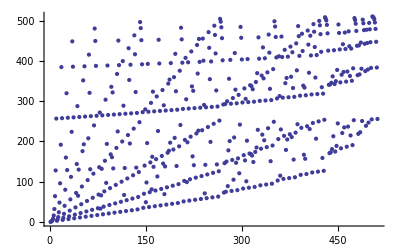

```mathematica
ListPlot[positions[s[[1]],8]]
```

A partir de 9 bits, on peut retrouver notre position ...

```mathematica
ref=s[[1]];
refpos=positions[s[[1]],8];
```

```mathematica
bitpos=79;
num=FromDigits[ref[[bitpos;;bitpos+8]],2]
```

33

```mathematica
Position[refpos,num][[1,1]]
bitpos
```

79

79

#### Statistiques ...

Et la largeur des bandes dans les pattern de DeBruijn?

```mathematica
s=sequence[8,30];
```

```mathematica
s[[1]]
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0,1,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,0,1,1,0,1,0,1,0,0,0,1,1,0,1,1,1,0,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,1,0,0,0,1,1,1,1,0,1,0,0,0,1,1,1,1,1,1,0,0,1,0,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,1,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,1,0,1,0,1,1,1,0,1,1,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
Sort[Tally[Length /@ Split[s⟦1⟧]]]
```

{{1,128},{2,64},{3,32},{4,16},{5,8},{6,4},{7,2},{8,1},{9,2}}

```mathematica
BarChart[%[[All,2]]]
```

Part::partd: Part specification %58 ⟦ All, 2 ⟧ is longer than depth of object.

BarChart::ldata: %58 ⟦ All, 2 ⟧ is not a valid dataset or list of datasets.

BarChart[%58⟦All,2⟧]

Tous les patterns ont une distribution de tailles de bandes dans le genre {taille, nombre} : {taille, 2^(9 - taille)}
Sauf pour la taille {d,0} et {d+1,2} ... pourquoi? heu...

```mathematica
s=sequence[8,1][[1]]
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0,1,0,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,0,1,1,0,1,0,1,0,0,0,1,1,0,1,1,1,0,0,0,1,1,1,0,0,1,0,0,0,1,1,1,0,1,1,0,0,0,1,1,1,1,0,1,0,0,0,1,1,1,1,1,1,0,0,1,0,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,1,1,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,1,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,1,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,1,0,1,1,1,0,1,0,1,1,1,0,1,1,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
Sort[positions[s,8]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511}

Moyenne de 2 voisins ...

```mathematica
s2=Round /@ N[Mean/@ Partition[s,3,1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,1,0,1,0,0,0,0,1,0,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0}

```mathematica
Sort[positions[s2,8]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,2,2,2,3,3,3,3,3,3,3,3,4,4,5,6,6,6,7,7,7,7,7,7,7,7,7,8,8,10,11,12,12,12,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,20,23,23,24,24,24,24,28,28,28,28,28,28,30,30,30,30,30,31,31,31,31,31,31,31,32,32,32,35,40,42,46,47,48,48,48,48,49,51,56,56,56,56,56,56,56,58,60,60,60,60,60,62,62,62,62,62,63,63,63,63,63,63,63,63,64,64,64,70,80,84,92,94,96,96,96,96,98,99,102,103,112,112,112,112,112,112,112,115,116,119,120,120,120,120,120,122,124,124,124,124,124,126,126,126,126,126,126,126,127,127,127,127,128,128,128,129,133,135,140,143,160,161,168,175,184,188,189,191,192,192,192,193,197,199,204,206,224,224,224,224,224,224,225,225,231,231,232,238,240,240,240,240,241,241,244,245,248,248,248,248,248,252,252,252,252,252,252,252,253,254,254,254,255,255,255,255,256,256,256,256,257,257,257,257,257,257,259,259,259,259,261,263,263,263,263,264,267,268,271,271,271,271,271,273,277,280,281,284,285,287,287,287,287,287,287,305,307,313,315,317,319,319,319,320,322,323,327,336,343,350,351,368,371,376,378,382,383,383,383,384,384,384,384,384,384,384,384,385,385,385,386,387,387,387,387,388,390,391,391,391,391,392,394,396,398,398,399,399,399,399,399,408,409,412,413,414,415,415,415,417,419,427,431,441,447,447,447,448,448,448,448,448,448,448,448,449,449,449,449,450,451,451,451,451,451,452,454,455,455,455,455,455,455,460,462,463,463,463,463,464,465,469,471,476,479,479,479,480,480,480,480,480,480,481,481,481,481,482,483,483,483,483,483,483,483,486,487,487,487,488,490,491,495,495,495,496,496,496,496,496,496,497,497,497,497,497,497,499,499,499,499,501,503,503,503,504,504,504,504,504,504,504,505,505,505,505,506,507,507,507,508,508,508,508,509,509,509,510,510,510,510,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511,511}

### Images de Debruijn pour generation rapide

#### 3 symboles a la fois (d = 2), nbs symboles, distance entre symbole voisin au moins 1

```mathematica
genseq[d_,nbs_,dist_]:=Module[{s,is},(
Print[nbs];
s=RandomSample[sequenceSingleBand[d,50,nbs,dist]];
is=ImageAdjust[Image[s],0,{0,nbs-1},{0,1}];
(*Export["debruijn_3x8.png",ImageAdjust[Image[s]],"PNG"]*)
is
)];
```

```mathematica
Timing[res2=Table[genseq[2,nbs,1],{nbs,2,16}]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

{15.605,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Export["debruijn_3bandes_"<>ToString[nbs]<>"sym.png",res2[[nbs-1]]],{nbs,2,16}]
```

{debruijn_3bandes_2sym.png,debruijn_3bandes_3sym.png,debruijn_3bandes_4sym.png,debruijn_3bandes_5sym.png,debruijn_3bandes_6sym.png,debruijn_3bandes_7sym.png,debruijn_3bandes_8sym.png,debruijn_3bandes_9sym.png,debruijn_3bandes_10sym.png,debruijn_3bandes_11sym.png,debruijn_3bandes_12sym.png,debruijn_3bandes_13sym.png,debruijn_3bandes_14sym.png,debruijn_3bandes_15sym.png,debruijn_3bandes_16sym.png}

```mathematica
ImageDimensions /@ res2
```

{{4,2},{14,6},{38,12},{82,20},{152,30},{254,42},{394,50},{578,50},{812,50},{1102,50},{1454,50},{1874,50},{2368,50},{2942,50},{3602,50}}

```mathematica
Timing[res3=Parallelize[Table[genseq[3,nbs,1],{nbs,2,11}]]]
```

2

5

3

4

8

6

7

10

9

11

{5.67235,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ImageDimensions /@ res3
```

{{5,2},{27,12},{111,36},{323,50},{753,50},{1515,50},{2747,50},{4611,50},{7293,50},{11003,50}}

```mathematica
Directory[]
```

/home/roys/svn3d/home/roys/math

```mathematica
Table[Export["debruijn_4bandes_"<>ToString[nbs]<>"sym.png",res3[[nbs-1]]],{nbs,2,11}]
```

{debruijn_4bandes_2sym.png,debruijn_4bandes_3sym.png,debruijn_4bandes_4sym.png,debruijn_4bandes_5sym.png,debruijn_4bandes_6sym.png,debruijn_4bandes_7sym.png,debruijn_4bandes_8sym.png,debruijn_4bandes_9sym.png,debruijn_4bandes_10sym.png,debruijn_4bandes_11sym.png}